# Ejercicio 2 - TP 01

Aplicación del método de Euler a las ec. de movimiento del oscilador armónico con condiciones iniciales dadas.

```mathematica
f[x_,p_,h_]:=x+h p (*evalúa x_j+1 usando x_j y p_j*)
g[x_,p_,h_]:=p-h x (*evalúa p_j+1 usando x_j y p_j*)
paso[x_,p_,h_]:={f[x,p,h], g[x,p,h]}
(*Para evaluar la función hay que poner el input como una lista:
paso[{1,1,0.1}]*)
```

```mathematica
tmax = 31
x0 = 1
p0 = 1
x = {x0}
p = {p0}
Do[
xnew = f[];
x = Append[x,xnew]; Print[xnew];
p =Append[p,pnew]; (* ; suprime el output*)
,{t,0,tmax}]
(*Do no tiene output*)
```

```mathematica
ListPlot[{x,p}]
```

{1,2,3}

{4,5,6}

{{1,2,3},{4,5,6}}

{{1,4},{2,5},{3,6}}

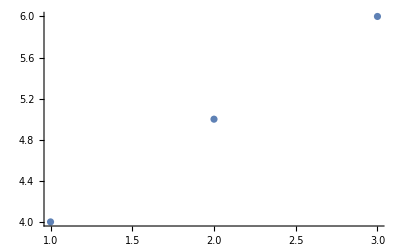

```mathematica
x = {1,2,3}
p = {4,5,6}
{x,p}
s = Transpose[{x,p}]
ListPlot[s]
```

```mathematica
ResourceFunction["MaTeXInstall"][]
```

ResourceFunction[MaTeXInstall][]

```mathematica
Needs["PacletManager`"]
PacletInstall["C:/Users/lupam/Downloads/MaTeX-1.7.8.paclet"]
```

```mathematica
Paclet["MaTeX","1.7.8",<>]
```

Paclet[MaTeX,1.7.8,<>]

```mathematica
MaTeX["\\sum_{k=1}^{\\infty} \\frac{1}{k}"]
```

MaTeX[\sum_{k=1}^{\infty} \frac{1}{k}]

```mathematica
<<MaTeX`
```

```mathematica
ConfigureMaTeX[
"Ghostscript"->"C:\\Program Files\\gs\\gs9.55.0\\bin\\gswin64c.exe"
]
```

{pdfLaTeX→C:\Users\lupam\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,CacheSize→100,WorkingDirectory→Automatic,Ghostscript→C:\Program Files\gs\gs9.55.0\bin\gswin64c.exe}

```mathematica
MaTeX["x^2", FontSize->16]
```

-Graphics-